```mathematica
ClearAll["Global`*"]
Quit[]
```

General approach is to include this code at the end on each process simulation.  Create a first order model function and evaluate it at several points.  Then, plot the specific points with the 20th order model.

1000

10

5

θ will be determined from the x-intercept.  k and s will be determined as described in B. Wayne Bequette's 'Process Dynamics' p. 191-210.

(1000 ⅇ^(-5 s))/(s (1+10 s))

1000 (1-ⅇ^((5-t)/10)) HeavisideTheta[-5+t]

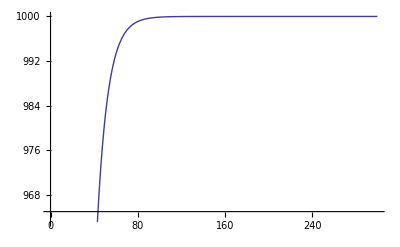

988.891

```mathematica
"General approach is to include this code at the end on each process simulation.  Create a first order model function and evaluate it at several points.  Then, plot the specific points with the 20th order model."
k=1000
τ=10
θ=5
"θ will be determined from the x-intercept.  k and s will be determined as described in B. Wayne Bequette's 'Process Dynamics' p. 191-210."
G[s_]=(k*Exp[-θ*s])/((τ*s+1)s)
S[t_]=InverseLaplaceTransform[G[s],s,t]
Plot[k(1-ⅇ^((τ-t)/τ)),{t,0,300}]
N[S[50]]
```

```mathematica
G[s_]=(kp*Exp[-θ*s])/((τ*s+1)s)
S[t_]=InverseLaplaceTransform[G[s],s,t]
```